```mathematica
X={1,1,0,0,0,1,1,2,1,1,1,0,2,2,4,3,2,0,2,2,2,2,3,1,0,2,0,5,3,6,2,1,2,1,8,11,5,8,12,15,22,48,50,73,92,108,113,149,123,97,75,34,6};
n=Length[X]
```

53

-8.70095+0.288207 t

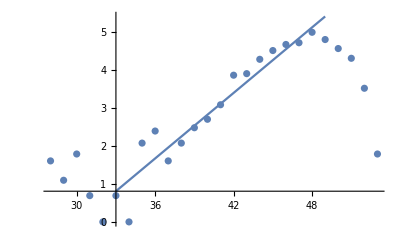

```mathematica
Fit[Table[{t,Log[X[[t]]]},{t,33,49}],{1,t},t]
Show[Plot[%,{t,33,49}],ListPlot[Table[{t,Log[X[[t]]]},{t,28,n}]],PlotRange->All]
```

```mathematica
Num=(Mean[Table[Log[X[[t]]] t,{t,33,49}]]-41Mean[Table[Log[X[[t]]],{t,33,49}]])/(Mean[Table[t^2,{t,33,49}]]-41^2)//N
```

0.288207

```mathematica
NSolve[ Sum[X[[t]] Exp[a*t] t,{t,33}]/Sum[Exp[2a*t] t,{t,33}]== Sum[X[[t]] Exp[a*t] ,{t,33}]/Sum[ Exp[2a*t],{t,33}],a,Reals]
```

{{a→0.036585}}

```mathematica
NSolve[ Sum[X[[t]] Exp[a*t] t,{t,48}]/Sum[Exp[2a*t] t,{t,48}]== Sum[X[[t]] Exp[a*t] ,{t,48}]/Sum[ Exp[2a*t],{t,48}],a,Reals]
```

{{a→0.226244}}